# 130B Quantum Physics

## Part I. Matrix Mechanics

## Introduction

### Everything is a Vector

#### What is Quantum Mechanics?

Quantum mechanics is a physics theory that describes the behavior of quantum systems (microscopic particles, strings, qubits ...).

What does physics theory do in general?

Describe the state of the system: a set of variables encoding the relevant information of the system.

Predict (i) the observables (measurement outcomes) and (ii) their dynamics (time evolution).

Physics theory is about encoding the physical reality in the form of information and generating predictions about the reality based on such information.

#### How to Encode Information?

State variables encode the information about the system. They are inferred from observations.

State variables may not have “physical meaning”.

Choice of state variables may not be unique. (There can be more than one way to describe a system.)

Example: how to describe the following images?

```mathematica
Block[{dat},
dat=ColorNegate/@RandomChoice[#,3]&/@GroupBy[ResourceData["MNIST","TestData"],Last->First];Grid[Partition[RandomSample@Flatten@Values@dat,6]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Image file: brightness of each pixel. - describe a state by all possible observables.

Human: digits 0, 1, 2, …, 9. - describe a state by a name.

Machine learning: feature vectors in the latent space. - describe a state by a vector in a vector space. [This is the most close to what we do in quantum mechanics.]

```mathematica
Block[{dat,imgs,pts},
dat=ColorNegate/@RandomChoice[#,3]&/@GroupBy[ResourceData["MNIST","TestData"],Last->First];
imgs=Flatten@Values@dat;
SeedRandom[449];
pts=Flatten[Table[#+ϵ,{ϵ,0.2RandomVariate[NormalDistribution[],{3,2}]}]&/@RandomVariate[NormalDistribution[],{10,2}],1];
pts=pts/Max[Norm/@pts];
Graphics[{{Arrow[{#,0}&/@{-1,1.2}],Text["feature 1",{1.2,0},{1,1}],Arrow[{0,#}&/@{-1,1.2}],Text["feature 2",{0,1.2},{1,-1},{0,1}]},Inset[#1,#2,{0,0},0.15]&@@@Thread[{imgs,pts}]},PlotRange->All,ImageSize->180]]
```

-Graphics-

In quantum mechanics, every state of a quantum system is described by a complex vector (an array of complex numbers).

The vector components are the state variables, and they may not need to have physical meanings. [They are also called probability amplitudes or wave amplitudes, but I don’t explain what is “waving” here.]

This particular (vector-based) approach of describing quantum states is not the only way. There are other ways to formulate quantum mechanics, just to name a few: density matrix formulation (matrix-based), classical shadow formulation (probability-based) [Reference], quantum bootstrap (observable-based) [Reference].

However, the vector description is a simple and efficient way to describe a (pure) state of a quantum system. So we will start from state vectors.

Information encoded in a quantum state is called quantum information. It provides the foundation for quantum computation/communication.

Hsin-Yuan Huang, Richard Kueng, John Preskill. arXiv:2002.08953.

Xizhi Han, Sean A. Hartnoll, Jorrit Kruthoff. arXiv:2004.10212.

#### What is a Vector?

Geometric interpretation: a vector (in high-school physics) is an arrow, used to represent a physical quantity that has both magnitude and direction.

Example: the displacement vector x in a two-dimensional coordinate space

```mathematica
DynamicModule[{x={0.6,0.8}},
Column[{LocatorPane[Dynamic[x],Graphics[{{AbsoluteThickness[1],LightGray,Dashed,Line[Dynamic[{{1,0}x,x}]],Line[Dynamic[{{0,1}x,x}]]},{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,3},{0,0},{-4,-3}}]]}}],
AbsoluteThickness[1],Arrow[{#,0}&/@{-1,1}],Arrow[{0,#}&/@{-1,1}],Text["\!\(x\_1\)",Dynamic[{1,0}x],{0,1}],Text["\!\(x\_2\)",Dynamic[{0,1}x],{1,0}],Text["0",{0,0},{1.5,1}]},{Arrowheads[0.1],Arrow[{{0,0},Dynamic[x]}]}},PlotRange->1,PlotRangePadding->0.02,ImageSize->120],Appearance->None],Style[Dynamic[StringTemplate["\!\(x=(x\_1,x\_2)=(`1`,`2`)\)"]@@x],"InlineFormula"]}]]
```

Algebraic interpretation: a vector (in computer science) is an array of numbers, serves as a data structure for storing and representing information.

Example 1: Color vector (the red/green/blue values form a vector)

RGBColor[{1, 0.5, 0.25}].rgb = [1., 0.5, 0.25] # [r, g, b]
RGBColor[{0.25, 0.5, 1}].rgb = [0.25, 0.5, 1.]

Example 2: Word vector (in natural language processing), vector representations of words that encode the meaning and semantics of the words.

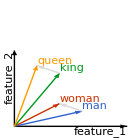

```mathematica
Block[{a={-0.2,0.1},b={-0.2,0.5},c={0.6,0.2}},Graphics[{{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,3},{0,0},{-4,-3}}]]}}],
AbsoluteThickness[1],Arrow[{#,0}&/@{0,1}],Arrow[{0,#}&/@{0,1}],Text["\!\(feature\_1\)",{1,0},{1,1}],Text["\!\(feature\_2\)",{0,1},{1,-1},{0,1}]},{#3,Arrowheads[{0.08}],Arrow[{{0,0},#1}],Text[#2,#1,{-1,-0.5}]}&@@@Thread[{{c,c+a,c+b,c+a+b},{"man","woman","king","queen"},{Blue,Red,Green,Orange}}],
{Arrowheads[{0.08}],LightGray,Arrow[{{c,c+a},{c+b,c+a+b}}]}},ImageSize->140]]
```

Use semantic relationship by vector arithmetic [Reference]:

king-man+woman=queen.

Vector in Quantum Mechanics:

The notion of state vector in quantum mechanics is closer to the algebraic interpretation --- it is used to encode the state of a quantum system, or to store the data of quantum information. There is no direct physical meaning associated with its amplitude and direction.

Real and complex vectors:

Real vector: an array of real numbers --- the space of n-component real vectors is denoted as ℝ^n

x=(x_1,x_2,…,x_n)∈ℝ^n.

Complex vector: an array of complex numbers --- the space of n-component complex vectors is denoted as ℂ^n

z=(z_1,z_2,…,z_n)∈ℂ^n.

They are just arrays of different data types. Compare to real vectors, complex vectors are more powerful data structures that can describe the wave behavior conveniently, and is therefore widely used in quantum mechanics.

Ekaterina Vylomova, Laura Rimell, Trevor Cohn, Timothy Baldwin. arXiv:1509.01692

### Complex Algebra

#### Complex Number

A complex number z is made of two real numbers (x,y) that combine with the real unit 1 and the imaginary unit ⅈ=√-1 respectively,

x∈ℝ, y∈ℝ→z=x+ⅈ y∈ℂ.

The real and imaginary units obey the following multiplication rules

1×1=1, 1×ⅈ=ⅈ×1=ⅈ, ⅈ×ⅈ=-1.

Addition:

{ | z=x+ⅈ y
w=u+ⅈ v→z +w=(x+u)+ⅈ (y+v)

Multiplication:

{ | z=x+ⅈ y
w=u+ⅈ v→z w=(x u-y v)+ⅈ (x v+y u)

Complex conjugate:

z=x+ⅈ y→z^*=x-ⅈ y.

Real and imaginary parts can be extracted from

Re z=1/2(z+z^*)=x,
Im z=1/(2ⅈ)(z-z^*)=y.

#### Complex Number in Mathematica

The imaginary unit ⅈ can be typeset in Mathematica by EsciEsc. For example, here is a complex number

```mathematica
3+1ⅈ
```

3+ⅈ

Multiplying two complex numbers together (Mathematica treats the space between two numbers as a multiplication operator just as a b=a×b in algebra)

```mathematica
(3+ⅈ)(4+2ⅈ)
```

10+10 ⅈ

Complex conjugation is given by

```mathematica
Conjugate[3+ⅈ]
```

3-ⅈ

Extract real and imaginary part by

```mathematica
Re[3+ⅈ]
Im[3+ⅈ]
```

3

1

#### Polar Complex Form

Through the Euler formula, a complex number z=x+ⅈ y may be written in a polar-coordinate form

z=|z|cos θ+ⅈ |z| sin θ=|z|ⅇ^(ⅈ θ).

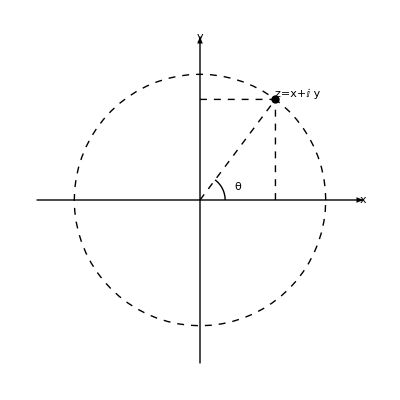

```mathematica
Graphics[{{Arrowheads[0.08],Arrow[1.3{-#,#}]&/@{{1,0},{0,1}}},{AbsoluteThickness[1],Dashed,Circle[{0,0},1],Line[{{0,0},{0.6,0.8}}],Line[{{0.6,0},{0.6,0.8}}],Line[{{0,0.8},{0.6,0.8}}]},{AbsolutePointSize[6],Point[{0.6,0.8}]},{Circle[{0,0},0.2,{0,ArcTan[0.6,0.8]}],Text["\!\(z=x+ⅈ y\)",{0.6,0.8},{-1,-1}],Text["θ",{0.3,0.1}]},Text["\!\(x\)",{1.3,0},{-1,0}],Text["\!\(y\)",{0,1.3},{0,-1}]},ImageSize->{Automatic,140}]
```

|z| - complex modulus (or magnitude)

(|z|)^2=z^*z=x^2+y^2.

(The complex conjugate is needed here to ensure (|z|)^2≥0.)

θ - complex argument (or phase)

arg z =θ=Im ln z=arctan y/x.

Complex numbers make it convenient to express the phase rotation by multiplication of phase factors ⅇ^(ⅈ θ), or addition of phase angles θ,

ⅇ^(ⅈ θ_1)ⅇ^(ⅈ θ_2)=ⅇ^(ⅈ (θ_1+θ_2)).

Complex conjugation simply flips the phase angle (θ→-θ),

(ⅇ^(ⅈ θ))^*=ⅇ^(-ⅈ θ).

### Linear Algebra

#### Matrix and Vector

A matrix is a two-dimensional array of numbers,

M=(M_11 | M_12 | ⋯
M_21 | M_22 | ⋯
⋮ | ⋮ | ⋱)∈ℂ^(m×n).

Matrix elements (components) M_ij are labeled by a row index i=1,…,m and a column index j=,1,…,n. Each component itself is a number. Let us consider M_ij∈ℂ to be general, such that the space of m-row n-column matrices will be denoted as ℂ^(m×n).

If m=n, the matrix is said to be a square matrix. In quantum mechanics, we will be mostly dealing with square matrices.

A vector can be viewed as a special case of a matrix.

Column vectors (multi-row single-column)

v=(v_1
v_2
⋮)∈ℂ^(n×1)≅ℂ^n.

Row vectors (single-row multi-column)

v=(v_1^* | v_2^* | ⋯)∈ℂ^(1×n)≅ℂ^n.

Column v.s. row: In terms of encoding information in n numbers, it doesn’t matter whether they are arranged in a column or a row. But when it comes to matrix-vector multiplication (to be discussed soon), there is a difference. So we use the v and v notation to distinguish them, instead of writing both as v.

#### Linear Superposition

Matrix (or vector) space. All m×n matrices forms a matrix space ℂ^(m×n). Its defining property is that any linear combination of matrices in the space is still a matrix in the same space (same applies to vectors)

∀A,B∈ℂ^(m×n);α,β∈ℂ:
α A+β B∈ℂ^(m×n)

A linear combination can be broken down into two types of basic operations:

Scalar multiplication:

A=(A_11 | A_12 | ⋯
A_21 | A_22 | ⋯
⋮ | ⋮ | ⋱)→α A=(α A_11 | α A_12 | ⋯
α A_21 | α A_22 | ⋯
⋮ | ⋮ | ⋱),

meaning that

(α A)_ij=α A_ij.

Addition:

A=(A_11 | A_12 | ⋯
A_21 | A_22 | ⋯
⋮ | ⋮ | ⋱),B=(B_11 | B_12 | ⋯
B_21 | B_22 | ⋯
⋮ | ⋮ | ⋱)
→A+B=(A_11+B_11 | A_12+B_12 | ⋯
A_21+B_21 | A_22+B_22 | ⋯
⋮ | ⋮ | ⋱),

meaning that

(A+B)_ij=A_ij+B_ij.

All these rules applies to vectors when matrices are single-column or single-row.

#### Matrix Multiplication

Matrix multiplication is an associative binary operation:

ℂ^(m×n)×ℂ^(n×l)→ℂ^(m×l),

meaning that two matrices can multiply if and only if the column dimension of the left matrix matches the row dimension of the right matrix.

Explicitly, when we write

(A_11 | A_12 | ⋯
A_21 | A_22 | ⋯
⋮ | ⋮ | ⋱)(B_11 | B_12 | ⋯
B_21 | B_22 | ⋯
⋮ | ⋮ | ⋱)=(C_11 | C_12 | ⋯
C_21 | C_22 | ⋯
⋮ | ⋮ | ⋱),

we mean that

C_ij=∑_k A_ik B_kj,

where k=1,…,n is the index to be contracted (to be summed over).

We can denote Eq. (DisplayFormulaNumbered) on the matrix level simply as

A B=C.

Matrix-vector multiplication: If one of the matrix is reduced to a vector, the above rules still apply. A matrix can left-multiply a column vector or right-multiply a row vector, if their contracted dimensions matches.

Left-multiplication

(A_11 | A_12 | ⋯
A_21 | A_22 | ⋯
⋮ | ⋮ | ⋱)(u_1
u_2
⋮)=(v_1
v_2
⋮)
⇒v_i=∑_j A_ij u_j,

Right-multiplication

(u_1 | u_2 | ⋯)(A_11 | A_12 | ⋯
A_21 | A_22 | ⋯
⋮ | ⋮ | ⋱)=(v_1 | v_2 | ⋯)
⇒v_j=∑_i u_i A_ij,

Vector-vector multiplication: If both matrices are reduced to vectors of the same dimension, we can define a inner product and a outer product between them.

Inner product

(u_1 | u_2 | ⋯)(v_1
v_2
⋮)=∑_i u_i v_i="a scalar (number)",

Outer product

(v_1
v_2
⋮)(u_1 | u_2 | ⋯)=(v_1 u_1 | v_1 u_2 | ⋯
v_2 u_1 | v_2 u_2 | ⋯
⋮ | ⋮ | ⋱).

Multiplying two row vectors or two column vectors are illegal (because dimensions do not match).

(u_1 | u_2 | ⋯)(u_1 | u_2 | ⋯)→No!
(v_1
v_2
⋮)(v_1
v_2
⋮)→No!

#### Identity Matrix and Kronecker Symbol

Identity matrix: a special n×n square matrix whose diagonal are all 1’s and off-diagonal are all 0’s. It looks like

𝟙=(1 | 0 | 0 | ⋯
0 | 1 | 0 | ⋱
0 | 0 | 1 | ⋱
⋮ | ⋱ | ⋱ | ⋱).

The matrix element of an identity matrix can be expressed using the Kronecker delta symbol δ_ij,

𝟙_ij=δ_ij≡Piecewise[{{1, i=j,}, {0, i≠j.}}]

Identity matrix multiplying on any vector keeps the vector unchanged, i.e. ∀u∈ℂ^n:u 𝟙=𝟙 u=u. This implies that the Kronecker delta has the following property

∑_i u_i δ_ij=u_j,
∑_j δ_ij u_j=u_i.

Rule of thumb: when δ_ij appears in a summation of i (or j), it annihilates with the summation symbol and replaces summation index i by j (or j by i) in the summand.

#### Matrix Algebra in Mathematica

Construct two matrices

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}};
B={{9,8,7},{6,5,4},{3,2,1}};
A//MatrixForm
B//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

(9 | 8 | 7
6 | 5 | 4
3 | 2 | 1)

Linear combine them simply as

```mathematica
A+B//MatrixForm
α A+β B//MatrixForm
```

(10 | 10 | 10
10 | 10 | 10
10 | 10 | 10)

(α+9 β | 2 α+8 β | 3 α+7 β
4 α+6 β | 5 α+5 β | 6 α+4 β
7 α+3 β | 8 α+2 β | 9 α+β)

Multiply them using “.” symbol, standing for the “dot product”.

```mathematica
A.B//MatrixForm
```

(30 | 24 | 18
84 | 69 | 54
138 | 114 | 90)

```mathematica
B.A//MatrixForm
```

(90 | 114 | 138
54 | 69 | 84
18 | 24 | 30)

Unlike multiplying two number (a b=b a, which is commutative), matrix multiplication is non-commutative, meaning that

A B≠B A,

for two square matrices A,B∈ℂ^(n×n) in general.

#### Matrix as a Machine

A matrix can be viewed as a machine that takes in a vector, acts (multiplies) on it, and returns a new vector.

Examples of 2×2 matrix M acting on 2-component vectors.

u→^M v=M u.

Exchanging the two components in the vector by

M=(0 | 1
1 | 0).

```mathematica
DynamicModule[{u={0.6,0.8},M={{0,1},{1,0}}},
Column[{LocatorPane[Dynamic[u],Graphics[{{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,3},{0,0},{-4,-3}}]]}}],
AbsoluteThickness[1],Arrow[{#,0}&/@{-1,1}],Arrow[{0,#}&/@{-1,1}],Text["0",{0,0},{1.5,1}]},{Arrowheads[0.1],Red,Arrow[{{0,0},Dynamic[u]}],Text["\!\(u\)",Dynamic[u],Dynamic[-0.5Normalize@u]]},{Arrowheads[0.1],Blue,Arrow[{{0,0},Dynamic[M.u]}],Text["\!\(v\)",Dynamic[M.u],Dynamic[-0.5Normalize@(M.u)]]}},PlotRange->1,PlotRangePadding->0.02,ImageSize->120],Appearance->None],Row[{Style[Dynamic[StringTemplate["\!\(u=(\*GridBox[{{`1`},{`2`}}])\)"]@@u],"InlineFormula"],
Style[Dynamic[StringTemplate["\!\(v=(\*GridBox[{{`1`},{`2`}}])\)"]@@(M.u)],"InlineFormula"]},Style["\!\(→\&M\)","InlineFormula"]]}]]
```

Reflecting the vector with respect to an axis by

M=(1 | 0
0 | -1).

```mathematica
DynamicModule[{u={0.6,0.8},M={{1,0},{0,-1}}},
Column[{LocatorPane[Dynamic[u],Graphics[{{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,3},{0,0},{-4,-3}}]]}}],
AbsoluteThickness[1],Arrow[{#,0}&/@{-1,1}],Arrow[{0,#}&/@{-1,1}],Text["0",{0,0},{1.5,1}]},{Arrowheads[0.1],Red,Arrow[{{0,0},Dynamic[u]}],Text["\!\(u\)",Dynamic[u],Dynamic[-0.5Normalize@u]]},{Arrowheads[0.1],Blue,Arrow[{{0,0},Dynamic[M.u]}],Text["\!\(v\)",Dynamic[M.u],Dynamic[-0.5Normalize@(M.u)]]}},PlotRange->1,PlotRangePadding->0.02,ImageSize->120],Appearance->None],Row[{Style[Dynamic[StringTemplate["\!\(u=(\*GridBox[{{`1`},{`2`}}])\)"]@@u],"InlineFormula"],
Style[Dynamic[StringTemplate["\!\(v=(\*GridBox[{{`1`},{`2`}}])\)"]@@(M.u)],"InlineFormula"]},Style["\!\(→\&M\)","InlineFormula"]]}]]
```

Rotating the vector by 90° counterclockwise by

M=(0 | -1
1 | 0).

```mathematica
DynamicModule[{u={0.6,0.8},M={{0,-1},{1,0}}},
Column[{LocatorPane[Dynamic[u],Graphics[{{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,3},{0,0},{-4,-3}}]]}}],
AbsoluteThickness[1],Arrow[{#,0}&/@{-1,1}],Arrow[{0,#}&/@{-1,1}],Text["0",{0,0},{1.5,1}]},{Arrowheads[0.1],Red,Arrow[{{0,0},Dynamic[u]}],Text["\!\(u\)",Dynamic[u],Dynamic[-0.5Normalize@u]]},{Arrowheads[0.1],Blue,Arrow[{{0,0},Dynamic[M.u]}],Text["\!\(v\)",Dynamic[M.u],Dynamic[-0.5Normalize@(M.u)]]}},PlotRange->1,PlotRangePadding->0.02,ImageSize->120],Appearance->None],Row[{Style[Dynamic[StringTemplate["\!\(u=(\*GridBox[{{`1`},{`2`}}])\)"]@@u],"InlineFormula"],
Style[Dynamic[StringTemplate["\!\(v=(\*GridBox[{{`1`},{`2`}}])\)"]@@(M.u)],"InlineFormula"]},Style["\!\(→\&M\)","InlineFormula"]]}]]
```

#### Eigen System of a Matrix

An eigen system of a n×n square matrix M refers to the set of eigenvalues λ^(k) and the corresponding eigenvectors u^(k) for k=1,…,n such that

M u^(k)=λ^(k)u^(k),

meaning that the multiplication of the matrix M to its eigenvector u^(k) can be reduced to the scalar multiplication by λ^(k).

Examples eigen systems of 2×2 matrices M.

Exchanging the two components in the vector by

M=(0 | 1
1 | 0).

```mathematica
DynamicModule[{u={0.6,0.8},M={{0,1},{1,0}},λs,us},
{λs,us}=Eigensystem[M];
us=Normalize/@us;
Column[{LocatorPane[Dynamic[u],Graphics[{{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,3},{0,0},{-4,-3}}]]}}],
AbsoluteThickness[1],Arrow[{#,0}&/@{-1,1}],Arrow[{0,#}&/@{-1,1}],Text["0",{0,0},{1.5,1}]},
{Arrowheads[0.1],Lighter[Black,0.6],Arrow[{{0,0},#2}],Text[StringTemplate["\!\(u\^(`1`)\)"][#1],#2,-0.5#2]}&@@@Thread[{{1,2},us}],
{Arrowheads[0.1],Red,Arrow[{{0,0},Dynamic[u]}],Text["\!\(u\)",Dynamic[u],Dynamic[-0.5Normalize@u]]},{Arrowheads[0.1],Blue,Arrow[{{0,0},Dynamic[M.u]}],Text["\!\(v\)",Dynamic[M.u],Dynamic[-0.5Normalize@(M.u)]]}},PlotRange->1,PlotRangePadding->0.02,ImageSize->120],Appearance->None],
Style[Grid[Prepend[Thread[{Range@Length@λs,λs,MatrixForm/@us}],{"\!\(k\)","\!\(λ\^(k)\)","\!\(u\^(k)\)"}],Dividers->{{2->True},{2->True}},Alignment->Center],"InlineFormula"]}]]
```

Reflecting the vector with respect to an axis by

M=(1 | 0
0 | -1).

```mathematica
DynamicModule[{u={0.6,0.8},M={{1,0},{0,-1}},λs,us},
{λs,us}=Eigensystem[M];
us=Normalize/@us;
Column[{LocatorPane[Dynamic[u],Graphics[{{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,3},{0,0},{-4,-3}}]]}}],
AbsoluteThickness[1],Arrow[{#,0}&/@{-1,1}],Arrow[{0,#}&/@{-1,1}],Text["0",{0,0},{1.5,1}]},
{Arrowheads[0.1],Lighter[Black,0.6],,Arrow[{{0,0},#2}],Text[StringTemplate["\!\(u\^(`1`)\)"][#1],#2,1.3{{0,-1},{1,0}}.#2+#2]}&@@@Thread[{{1,2},us}],
{Arrowheads[0.1],Red,Arrow[{{0,0},Dynamic[u]}],Text["\!\(u\)",Dynamic[u],Dynamic[-0.5Normalize@u]]},{Arrowheads[0.1],Blue,Arrow[{{0,0},Dynamic[M.u]}],Text["\!\(v\)",Dynamic[M.u],Dynamic[-0.5Normalize@(M.u)]]}},PlotRange->1,PlotRangePadding->0.02,ImageSize->120],Appearance->None],
Style[Grid[Prepend[Thread[{Range@Length@λs,λs,MatrixForm/@us}],{"\!\(k\)","\!\(λ\^(k)\)","\!\(u\^(k)\)"}],Dividers->{{2->True},{2->True}},Alignment->Center],"InlineFormula"]}]]
```

Rotating the vector by 90° counterclockwise by

M=(0 | -1
1 | 0).

```mathematica
DynamicModule[{u={0.6,0.8},M={{0,-1},{1,0}},λs,us},
{λs,us}=Eigensystem[M];
us=Normalize/@us;
Column[{LocatorPane[Dynamic[u],Graphics[{{Arrowheads[{{0.01,1,Graphics[Line[Offset/@{{-4,3},{0,0},{-4,-3}}]]}}],
AbsoluteThickness[1],Arrow[{#,0}&/@{-1,1}],Arrow[{0,#}&/@{-1,1}],Text["0",{0,0},{1.5,1}]},
{Arrowheads[0.1],Dashed,{Lighter[Orange,0.5],Arrow[{{0,0},#2}],Text[StringTemplate["\!\(Re u\^(`1`)\)"][#1],#2,1.6{{0,-1},{1,0}}.#2+(-1+1.5#1)#2]}&@@@Thread[{{1,2},Re[us]}],
{Lighter[Cyan,0.5],Arrow[{{0,0},#2}],Text[StringTemplate["\!\(Im u\^(`1`)\)"][#1],#2,1.6{{0,-1},{1,0}}.#2+#2]}&@@@Thread[{{1,2},Im[us]}]},
{Arrowheads[0.1],Red,Arrow[{{0,0},Dynamic[u]}],Text["\!\(u\)",Dynamic[u],Dynamic[-0.5Normalize@u]]},{Arrowheads[0.1],Blue,Arrow[{{0,0},Dynamic[M.u]}],Text["\!\(v\)",Dynamic[M.u],Dynamic[-0.5Normalize@(M.u)]]}},PlotRange->1,PlotRangePadding->0.02,ImageSize->120],Appearance->None],
Style[Grid[Prepend[Thread[{Range@Length@λs,λs,MatrixForm/@us}],{"\!\(k\)","\!\(λ\^(k)\)","\!\(u\^(k)\)"}],Dividers->{{2->True},{2->True}},Alignment->Center],"InlineFormula"]}]]
```

##### Finding eigen systems in Mathematica

```mathematica
M={{0,1},{1,0}};
M//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
Eigensystem[M]
```

{{-1,1},{{-1,1},{1,1}}}

```mathematica
M.{-1,1}
```

{1,-1}

```mathematica
M.{1,1}
```

{1,1}

## Quantum States

### Ket and Bra

#### Ket Vector

Postulate 1 (States): States of a quantum system are described as vectors in the associated Hilbert space.

In quantum mechanics, every state of a quantum system is described by a complex column vector, denoted by a ket (or ket state, ket vector) v in Dirac’s notation,

v≏(v_1
v_2
⋮),

where v_1,v_2,…∈ℂ. The length of the vector depends on the dimension of the vector space.

Note: “≏” implies the vector representation is basis dependent and the values of vector components may change if we view the same state in a different basis.

To write down the vector representation, we must specified a set of (orthonormal) basis vectors in the vector space, and represent them as one-hot unit vectors:

1≏(1
0
⋮),2≏(0
1
⋮), ….

Such that v can be expressed as a linear combination of basis vectors

v=v_1 1+v_2 2+…
=∑_i v_i i.

The ith vector component v_i is the linear combination coefficient in front of the ith basis vector i.

Superposition Principle: any linear combination of quantum states of a given quantum system is still a valid quantum state of the same system.

#### Bra Vector

Every ket v has a dual vector, called bra v, a complex row vector. They are related by conjugate transpose with respect to each other.

v≏(v_1
v_2
⋮)↔^dual v=(v_1^* | v_2^* | ⋯).

The name comes from the fact that they combine into a bracket, which represents a scalar product [to be introduced later].

Every basis vector i also has a dual basis vector i, the are represented as

1≏(1 | 0 | ⋯),
2≏(0 | 1 | ⋯),
⋯.

The dual basis vectors form a set of basis for the bra vector. In terms of basis vectors,

v=v_1^*1+v_2^*2+…
=∑_i v_i^*i.

The ith vector component v_i^* is the linear combination coefficient in front of the ith dual basis vector i.

#### Qubit System

A qubit (or quantum-bit) is a quantum system that has two distinct states.

The two distinct states are 0 and 1.

We can choose 0 and 1 to be the basis vectors (like choosing a coordinate system) and write:

0≏(1
0), 1≏(0
1)

The vector representation of a quantum state is also called a state vector.

By saying that a qubit is a two-state system, its state vector has two components.

A generic quantum state of a qubit is a complex linear superposition of the basis states

ψ=ψ_0 0+ψ_1 1≏(ψ_0
ψ_1).

ψ_0,ψ_1∈ℂ are complex numbers. They parameterize the state ψ.

Conversely, every two-component complex vector describes a qubit state.

Statistical interpretation: (|ψ_0|)^2 and (|ψ_1|)^2 are respectively the probabilities to observe the qubit in the 0 and the 1 states.

There is a dual bra vector ψ associated with each ket vector ψ,

ψ=ψ_0^*0+ψ_1^*1≏(ψ_0^* | ψ_1^*),

which, the bra state, encodes the same information about the qubit as the ket state. They are equally good description of the quantum state of a qubit (but play different roles in defining the scalar product, as to be discussed soon).

### Scalar Product

#### Definition

Scalar product (or inner product) is a function that takes two ket vectors, u and v,

u≏(u_1
u_2
⋮),v≏(v_1
v_2
⋮),

and returns a complex number, denoted by the bracket uv,

uv≏(u_1^* | u_2^* | ⋯)(v_1
v_2
⋮)
=u_1^*v_1+u_2^*v_2+…
=∑_i v_i^*w_i.

Exchanging the two states in a scalar product lead to a complex conjugation of result

vu=uv^*.

Scalar product of any vector v with itself is real and positive definite,

vv>=0.

More specifically,

vvPiecewise[{{=0, if v=0}, {>0, otherwise}}].

This implies the Cauchy-Schwarz inequality

(|uv|)^2<=uuvv.

Prove Eq. (DisplayFormulaNumbered).

(i) Trivial case: when v=0 is a zero vector,

uv= vv=0,

Eq. (DisplayFormulaNumbered) trivially holds as an equality.

(ii) Non-trivial case: when v≠0, i.e.  vv>0. Let

w=uvv-vvu,

one can show that

ww=(vvu-uvv)(uvv-vvu)
=vvuuvv-vvuvvu-uvvuvv+uvvvvu
=vv(uuvv-uvvu).

Given that vv>0, we have

uuvv-uvvu=ww/vv>=0,

as ww≥0 following from Eq. (DisplayFormulaNumbered). This proves the inequality Eq. (DisplayFormulaNumbered), as

(|uv|)^2=uvvu≤uuvv.

Hilbert space: the space of all ket vectors together with their scalar product structure, denoted as ℋ, which is the space of all possible quantum states of a system.

#### Normalization

Squared norm of a vector v is the scalar product of the vector with itself, denoted as

(‖v‖)^2=vv.

Taking off the square, ‖v‖=√vv is the norm of v.

Normalized state: a state v is normalized ⇔ Its norm is one, i.e.

(‖v‖)^2=vv=∑_i (|v_i|)^2=1.

Example: Consider a qubit state

v≏(v_0
v_1),

the normalization condition means

vv=v_0^*v_0+v_1^*v_1=1.

In general, the normalization condition means

vv=∑_i (|v_i|)^2=1.

According to the statistical interpretation of quantum state, (|v_i|)^2 is the probability to observe the system in the ith basis state. The normalization condition is simply a requirement that the probabilities must sum up to unity.

Normalization of a state: if a state v was not normalized, it can be normalized by

v->v/(‖v‖)=1/(√vv)v,

unless ‖v‖ is zero or infinity.

Normalize the vector v≏(1
2ⅈ).

Step 1: calculate the norm

vv=(1 | -2ⅈ)(1
2ⅈ)=1+4=5.
√vv=√5.

Step 2: divide the vector by the norm

v->1/(√vv)v
≏1/(√5)(1
2ⅈ).

#### Orthogonality

Orthogonal states: two states u and v are orthogonal to each other ⇔ their scalar product is zero, i.e.

uv⟩=∑_i u_i^*v_i=0.

For example, the qubit states |0⟩ and |1⟩ (see Eq. (DisplayFormulaNumbered)) are orthogonal, as

01=(1 | 0)(0
1)=0.

|0⟩ and |1⟩ are orthogonal for a good reason: they are distinct states of a qubit, i.e. if the qubit is in state 0, it is definitely not in state 1, vice versa.

### Basis and Hilbert Space

#### Orthonormal Basis

Orthonormal basis: a (ordered) set of kets

ℬ={i:i=1,2,…,n},

in which the  vectors are normalized by themselves and orthogonal to each other:

ij=δ_ij≡Piecewise[{{1, i=j,}, {0, i≠j.}}]

Each orthogonal basis state describes a distinct reality of the quantum system.

Orthonormal basis states are represented by one-hot vectors, as they are normalized and orthogonal to each other

1≏(1
0
0
⋮), 2≏(0
1
0
⋮), 3≏(0
0
1
⋮), ….

Choosing a basis is always a helpful practice in quantum mechanics. But quantum mechanics can be formulated in a basis independent manner.

#### Hilbert Space

A set of orthonormal basis spans a Hilbert space (the vector space of kets), denoted as

ℋ=span ℬ=span {i:i=1,2,…,n}.

The dimension of the vector space dim ℋ = the number n of basis vectors = the maximal number of linearly independent vectors in the space.

The Hilbert space dimension of a quantum system can be finite or infinite. Example: a qubit - dim ℋ=2, ten qubits - dim ℋ=2^10=1024, a particle in a continuous space - dim ℋ=∞.

Dimension of the Hilbert space is often a choice: we don’t really know how many independent states are there in a quantum system. We only care about the states that are relevant to us.

Example: 0 and 1 form an orthonormal basis of the qubit Hilbert space. They represent two distinct realities: if the qubit is in state 0, it is definitely not in state 1 (and vice versa).

#### State Basis Expansion

Completeness: Any full set of distinct states in the Hilbert space ℋ forms a complete set of orthonormal basis ℬ, such that every state v∈ℋ can be expanded as a linear superposition of the basis states,

v=v_1 1+v_2 2+…=∑_i v_i i.

Each basis state i describes a distinct reality that the quantum system can realize under observation.

The superposition coefficient v_i are the components of the state vector, which can be extracted by the scalar product with the basis state,

v_i=iv.

Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) can be written in a more elegant form in terms of bras and kets only

v=∑_i iiv.

Statistical interpretation: If a quantum system is known to be in a superposition state v=∑_i v_i i of distinct realities described by orthogonal states i (i=1,2,…), an observation designed to discern which reality the system is really in will find the system in the state i with the probability

p(i|v)=(|v_i|)^2=(|iv|)^2.

### Born’s Rule

#### Fidelity

The fidelity F(u,v) between two quantum states u and v quantifies the similarity (overlap) between two states. It is given by the squared absolute value of their scalar product (assuming the normalization of state vectors)

F(u,v)=(|uv|)^2.

Fidelity is symmetric: F(u,v)=F(v,u).

Fidelity takes values in the range of

0<=F(u,v)≤1.

This follows from the Cauchy-Schwarz inequality of scalar product Eq. (DisplayFormulaNumbered) that (|uv|)^2<=uuvv.

#### Statistical Interpretation

Hypothesis testing: If a quantum system is prepared in a state v, an observation designed to check whether the system is in the state u will return a confirmative result with probability

p(u|v)=(|uv|)^2.

Detailed balance: the probability to observe one state given another is the same as the other way round, both are given by their fidelity

p(u|v)=p(v|u)=F(u,v)=(|uv|)^2.

Identical states. Two states u and v are identical iff the fidelity between them is one (fully overlap)

(|uv|)^2=1.

This is only achievable when

u=ⅇ^(ⅈ φ)v,

i.e. the two states are the same up to phase ambiguity.

Reality must be confirmable by repeated observations: if a quantum system is known to be in a state v, observing the system again will certainly confirm the state v (with probability 1).

Distinct states. Two states u and v are distinct iff the fidelity between them is zero (no overlap)

(|uv|)^2=0.

Orthogonal states ⇔ distinct realities.

Distinct realities are distinguishable by repeated observations: if a quantum system is known to be in a state v, observing the system again will certainly not find the system in another orthogonal state u.

Overlapping states. In general, two different states u and v may have partial overlap (they don’t need to be orthogonal), i.e. their fidelity falls between zero and one

0<(|uv|)^2<1.

Realities can overlap: if two quantum states are more similar to (more overlapped with) each other, the probability to confuse them is higher.

"3"≏-Graphics-, "5"≏-Graphics-.

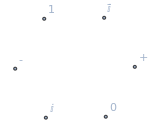
{0, 1}, {+, -}, and {ⅈ, ⅈ̄} are three pairs of distinct states of a qubit (i.e. 2-dimensional Hilbert space). Within each pair, the two states are orthogonal. However, any two states from different pairs have 50% overlap (i.e. 1/2 fidelity). Their overlapping relations can be visualized as the following graph.    
-Graphics-
Can you figure out an assignment of 2-component vector representation for these states that is consistent with their overlapping relations? 
[Hint: read Lecture 2 of [Reference]]
[Comment: This result shows how it is possible to embed so many different realities just in a 2-dimensional Hilbert space.]

Leonard Susskind, Art Friedman. Quantum Mechanics - the Theoretical Minimum. Publisher: Basic Books (2014).

## Quantum Operators

### Matrix Representation

#### Definition

Operator: an operator acts on a state and returns a new state.

Ô | : | ℋ | → | ℋ
  |   | v | ↦ | w=Ô v

Identity operator is a special operator that maps any state to itself (the do-nothing operator), denoted as 𝟙.

∀v: 𝟙v=v.

#### Operator Acting on State

Recall: a matrix multiplying on a vector produces a new vector. If every quantum state is described by a vector, one may conjecture that every quantum operator should be described by a (square) matrix. --- This is indeed a basic assumption of quantum mechanics: states are to be operated (transformed) linearly.

Applying an operator to a state ≏ multiplying a matrix to a vector.

w | = | Ô | v
↓^≏ |   | ↓^≏ | ↓^≏
(w_1
w_2
⋮) | = | (O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱) | (v_1
v_2
⋮)

or equivalently

w_i=∑_j O_(i,j)v_j.

The matrix element O_ij tells how the operator should act on each basis states: the operator Ô will turn a basis state j to a superposition state of basis states i with superposition coefficients O_ij.

Ô j=∑_i O_ij i.

Show Eq. (DisplayFormulaNumbered) as a result of Eq. (DisplayFormulaNumbered) using one-hot representation for basis vectors.

Use the matrix and vector representations of the operator and basis state

Ô 1≏(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱) | (1
0
⋮)=(O_11
O_21
⋮),
Ô 2≏(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱) | (0
1
⋮)=(O_12
O_22
⋮),
…

Therefore the state Ô j corresponds to the vector along the j-column in the matrix representation of Ô, i.e.

Ô j≏(O_(1j)
O_(2j)
⋮)
=O_(1j)(1
0
⋮)+O_(2j)(0
1
⋮)+…
≏O_(1j)1+O_(2j)2+…
=∑_i O_ij i

In other words, O_ij is the amplitude to transform basis state j to basis state i under the action of the operator Ô. It is sufficient to specify the operator by specifying its action on basis states, as all possible states are just linear combination of basis states, and the operator acts linearly.

#### Operator Basis Expansion

Given an orthonormal basis  ℬ={i:i=1,2,…} of the Hilbert space ℋ, every operator Ô acting in ℋ can be expanded as a linear combination of basis operators ij,

Ô=∑_(i,j) i O_(i,j)j,

ij denotes the operator that targets the state j and transforms it to the state i, because

(ij)k=ijk=i δ_(j,k)
=Piecewise[{{i, if k=j,}, {0, if k≠j.}}]

Thus Eq. (DisplayFormulaNumbered) is consistent with the Eq. (DisplayFormulaNumbered) in describing how the operator Ô acts on the state.

O_(i,j)∈ℂ are complex coefficients, which can be extracted by

O_(i,j)=i Ô j.

Prove Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered) using the orthonormal property of the basis vectors, without representing them as on-hot vectors explicitly.

i Ô j=i(∑_(k,l) k O_(k,l)l)j
=∑_(k,l) ik O_(k,l)lj
=∑_(k,l) δ_(i,k)O_(k,l)δ_(l,j)
=O_(i,j).

Alternatively, ij can be represented as an one-hot matrix that is zero everywhere with a single 1 at the row-i column-j. For example, in a 2-dimensional Hilbert space [recall Eq. (DisplayFormulaNumbered) for how to outer product two vectors]

11≏(1
0)(1 | 0)=(1 | 0
0 | 0),
12≏(1
0)(0 | 1)=(0 | 1
0 | 0),
21≏(0
1)(1 | 0)=(0 | 0
1 | 0),
22≏(0
1)(0 | 1)=(0 | 0
0 | 1).

Therefore, Eq. (DisplayFormulaNumbered) indeed reconstructs the matrix representation

O_11 11+O_12 12+O_21 21+O_22 22
≏(O_11 | O_12
O_21 | O_22).

The above can be generalized to larger matrices (higher dimensions).

Matrix representation. Every operator Ô can be represented as a matrix

Ô≏(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱).

The ith row jth column matrix element O_(i,j) describes:

The linear combination coefficient in front of the basis operator ij, as in Eq. (DisplayFormulaNumbered).

The amplitude to transform state j to state i under the action of the operator Ô, as in Eq. (DisplayFormulaNumbered).

#### Examples of Operators

Example I: Identity operator

Identity operator is universally represented by the identity matrix in any orthonormal basis (independent of the basis choice).

According to Eq. (DisplayFormulaNumbered),

𝟙_ij=i𝟙j=ij=δ_ij=Piecewise[{{1, i=j}, {0, i≠j}}].

In matrix representation Eq. (DisplayFormulaNumbered),

𝟙=(1 |   |  
  | 1 |  
  |   | ⋱).

Using Dirac notation Eq. (DisplayFormulaNumbered),

𝟙=∑_(i,j) i 𝟙_ij j=∑_(i,) ii.

This is also call the resolution of identity.

Example II: Pauli operators

Pauli operators are a set of operators acting on a qubit.

(σ̂)^x=10+01,
(σ̂)^y=ⅈ 10-ⅈ01,
(σ̂)^z=00-11,

Sometimes the identity operator

𝟙=00+11,

is also included as the 0th Pauli operator.

Pauli matrices - matrix representations of Pauli operators on the qubit basis {0,1}:

𝟙≏(1 | 0
0 | 1),(σ̂)^x≏(0 | 1
1 | 0), (σ̂)^y≏(0 | -ⅈ
ⅈ | 0), (σ̂)^z≏(1 | 0
0 | -1).

### Operator Algebra

#### Operator Product

Product (or composition) of two operators Ô and P̂ is a combined operator Ô P̂ that first applies P̂ to the sate then applies Ô (from right to left):

(Ô P̂)v=(Ô(P̂ v)).

Composing two operators ≏ multiplying two matrices.

Ô P̂≏(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱)(P_11 | P_12 | ⋯
P_21 | P_22 | ⋯
⋮ | ⋮ | ⋱).

Prove Eq. (DisplayFormulaNumbered) using Eq. (DisplayFormulaNumbered).

Ô P̂=(∑_ij i O_ij j)(∑_kl k P_kl l)
=∑_(ij,kl) i O_ij jk P_kl l
=∑_(ij,kl) i O_ij δ_(j,k)P_kl l
=∑_ijl i O_ij P_jl l
=∑_il i(∑_j O_ij P_jl)l
=∑_ij i(∑_k O_ik P_kj)j.

Operator product is non-commutative in general, i.e.

Ô P̂≠P̂ Ô.

#### Single-Qubit Pauli Operators

Example: product of Pauli operators

Multiplication table

| 𝟙 | (σ̂)^x | (σ̂)^y | (σ̂)^z
𝟙 | 𝟙 | (σ̂)^x | (σ̂)^y | (σ̂)^z
(σ̂)^x | (σ̂)^x | 𝟙 | ⅈ (σ̂)^z | -ⅈ (σ̂)^y
(σ̂)^y | (σ̂)^y | -ⅈ (σ̂)^z | 𝟙 | ⅈ (σ̂)^x
(σ̂)^z | (σ̂)^z | ⅈ (σ̂)^y | -ⅈ (σ̂)^x | 𝟙

Verify Eq. (DisplayFormulaNumbered) by multiplying Pauli matrices defined in Eq. (DisplayFormulaNumbered).

```mathematica
TableForm[Table[MatrixForm[PauliMatrix[a].PauliMatrix[b]],{a,0,3},{b,0,3}],TableHeadings->({#,#}&@{"𝟙","\!\(σ\^x\)","\!\(σ\^y\)","\!\(σ\^z\)"})]
```

| 𝟙 | σ^x | σ^y | σ^z
𝟙 | (1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | -ⅈ
ⅈ | 0) | (1 | 0
0 | -1)
σ^x | (0 | 1
1 | 0) | (1 | 0
0 | 1) | (ⅈ | 0
0 | -ⅈ) | (0 | -1
1 | 0)
σ^y | (0 | -ⅈ
ⅈ | 0) | (-ⅈ | 0
0 | ⅈ) | (1 | 0
0 | 1) | (0 | ⅈ
ⅈ | 0)
σ^z | (1 | 0
0 | -1) | (0 | 1
-1 | 0) | (0 | -ⅈ
-ⅈ | 0) | (1 | 0
0 | 1)

The table Eq. (DisplayFormulaNumbered) can be summarized in a single formula: the product of Pauli matrices (as the defining property of Pauli matrices)

(σ̂)^a(σ̂)^b=δ^ab 𝟙+ⅈ ϵ^abc(σ̂)^c,

where a,b,c=x,y,z.

δ^ab denotes the Kronecker delta symbol, defined as

δ^ab=Piecewise[{{1, if a=b}, {0, if a≠b}}]

ϵ^abc denotes the Levi-Civita symbol, defined as

ϵ^abc=Piecewise[{{1, if (a b c) is a cyclic of (x y z)}, {-1, if (a b c) is a cyclic of (z y x)}, {0, otherwise}}]

Another version of Eq. (DisplayFormulaNumbered) using vector notation

(m·σ̂) (n·σ̂)=(m·n) 𝟙+ⅈ (m×n)·σ̂,

where m,n are three-component vectors (each component is a scalar).

The generalized vector σ̂ should be understood as a vector of matrices, or as a three-dimensional tensor (shape: 3×2×2).

Here m·σ̂ means

m·σ̂=m_x(σ̂)^x+m_y(σ̂)^y+m_z(σ̂)^z
≏(m_z | m_x-ⅈ m_y
m_x+ⅈ m_y | -m_z).

As we contract a 3-component vector m with a 3×2×2-component tensor σ̂ along the first index (the dimension 3 index), the result is a 2×2 matrix.

Repeatedly applying Eq. (DisplayFormulaNumbered) enables us to product more Pauli operators together. For example

(l·σ̂) (m·σ̂) (n·σ̂)=ⅈ l·(m×n)𝟙+ ((m·n)l-(l·n) m+(l·m) n)·σ̂ .

Derive Eq. (DisplayFormulaNumbered).

(l·σ̂) (m·σ̂) (n·σ̂)=(l·σ̂) ((m·n) 𝟙+ⅈ (m×n)·σ̂)
=(m·n) (l·σ̂)+ⅈ (l·σ̂) (m×n)·σ̂
=(m·n) (l·σ̂)+ⅈ (l·(m×n)𝟙+ⅈ (l×(m×n))·σ̂)
=ⅈ l·(m×n)𝟙+ ((m·n) l-l×(m×n))·σ̂
=ⅈ l·(m×n)𝟙+((m·n)l-(l·n) m+(l·m) n)·σ̂

Here we have used the vector triple product formula: 
l×(m×n)=(l·n)m-(l·m)n

#### Commutator

Commutator of two operators Ô and P̂

[Ô,P̂]=Ô P̂-P̂ Ô.

Commutator is antisymmetric, [Ô,P̂]=-[P̂,Ô].

As a result, commutator of an operator with itself always vanishes [Ô,Ô]=0.

If the commutator vanishes [Ô,P̂]=0, we say that the two operators Ô and P̂ commute, i.e. Ô P̂=P̂ Ô (operators can pass though each other as if they were numbers) ⇒ it does not matter which operator is applied first, the consequence will be the same.

Example: dressing up to school.

A: put on the socks,

B: put on the shoes,

C: put on the hat,

A and B do not commute (changing the order leads to different result). But A and C commute, B and C also commute (changing the order does not affect the result).

Useful rules to evaluate commutators

Bi-linearity:

[Ô,P̂+Q̂]=[Ô,P̂]+[Ô,Q̂],
[Ô+P̂,Q̂]=[Ô,Q̂]+[P̂,Q̂].

Prove Eq. (DisplayFormulaNumbered).

Prove the right linearity:

[Ô,P̂+Q̂]=Ô (P̂+Q̂)-(P̂+Q̂)Ô
=Ô P̂+Ô Q̂-P̂ Ô-Q̂ Ô
=Ô P̂-P̂ Ô+Ô Q̂-Q̂ Ô
=[Ô,P̂]+[Ô,Q̂].

Similar prove for the left linearity.

Product rules:

[Ô,P̂ Q̂]=[Ô,P̂]Q̂+P̂ [Ô,Q̂],
[Ô P̂,Q̂]=[Ô,Q̂]P̂+Ô [P̂,Q̂].

Prove Eq. (DisplayFormulaNumbered).

[Ô,P̂ Q̂]=Ô P̂ Q̂-P̂ Q̂ Ô
=Ô P̂ Q̂-P̂ Ô Q̂+P̂ Ô Q̂-P̂ Q̂ Ô
=(Ô P̂ -P̂ Ô)Q̂+P̂ (Ô Q̂-Q̂ Ô)
=[Ô,P̂]Q̂+P̂ [Ô,Q̂]

Similarly for the other line.

Example: Commutators of Pauli operators

[(σ̂)^x,(σ̂)^y]=2ⅈ (σ̂)^z,
[(σ̂)^y,(σ̂)^z]=2ⅈ (σ̂)^x,
[(σ̂)^z,(σ̂)^x]=2ⅈ (σ̂)^y.

Or more compactly as

[(σ̂)^a,(σ̂)^b]=2ⅈ ϵ^abc(σ̂)^c,

for a,b,c=x,y,z, using the Levi-Civita symbol ϵ^abc defined in Eq. (DisplayFormulaNumbered).

Eq. (DisplayFormulaNumbered) can be considered as the defining algebraic properties of single-qubit operators (Pauli matrices). Or even more compactly expressed using the cross product of vectors

σ̂×σ̂=2ⅈ σ̂.

#### Operator Function

Operator power. nth power of an operator Ô is the composition of Ô by n times.

(Ô)^n=Ô Ô…(n times)…Ô.

Operator function. Given a function f(x) that admits Taylor expansion

f(x)=∑_n c_n x^n,

the corresponding operator function is defined as

f(Ô)=∑_n c_n(Ô)^n,

with the same set of coefficients c_n.

f(Ô) is still an operator that can act on states in ℋ.

Operator exponential. Given the exponential function

ⅇ^x=1+x+x^2/(2!)+…=∑_(n=0)^∞ 1/(n!)x^n,

the exponential of an operator is defined as

ⅇ^(Ô)=𝟙+Ô+(Ô)^2/(2!)+…=∑_(n=0)^∞ 1/(n!)(Ô)^n,

Note: exponentiating an matrix is NOT exponentiating each of the matrix element.

Example: exponentiating a Pauli matrix

Given (σ̂)^y≏(0 | -ⅈ
ⅈ | 0), 
show that the matrix representation of ⅇ^(ⅈ θ (σ̂)^y) is 
ⅇ^(ⅈ θ (σ̂)^y)≏(cos θ | sin θ
-sin θ | cos θ).

Method I: Mathematica

ⅇ^(ⅈ θ (σ̂)^y)≏e^(0 | θ
-θ | 0)=(cos θ | sin θ
-sin θ | cos θ).

```mathematica
MatrixExp[{{0,θ},{-θ,0}}]
```

{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}

Method II: Taylor expansion.

ⅇ^(ⅈ θ (σ̂)^y)=∑_n 1/(n!)(ⅈ θ (σ̂)^y)^n
=∑_n (ⅈ θ)^n/(n!)((σ̂)^y)^n

Note that

((σ̂)^y)^n=Piecewise[{{𝟙, if n is even,}, {(σ̂)^y, if n is odd.}}]

So

ⅇ^(ⅈ θ (σ̂)^y)=∑_m (ⅈ θ)^(2m)/((2m)!)((σ̂)^y)^(2m)+∑_m (ⅈ θ)^(2m+1)/((2m+1)!)((σ̂)^y)^(2m+1)
=∑_m (ⅈ θ)^(2m)/((2m)!)𝟙+∑_m (ⅈ θ)^(2m+1)/((2m+1)!)(σ̂)^y
=cos θ 𝟙+ⅈ sin θ (σ̂)^y
≏(cos θ | sin θ
-sin θ | cos θ).

Use the definition Eq. (DisplayFormulaNumbered) to prove that 
exp(ⅈ θ n·σ̂)=cos(θ)𝟙+ⅈ sin(θ) n·σ̂ 
given that n is a 3-component real unit vector.

#### Operator Trace

The trace of an operator Ô is defined as

Tr Ô=∑_i i Ô i.

The result is a scalar.

On the matrix level, taking the trace is simply summing over diagonal matrix elements

Tr(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱)=O_11+O_22+…=∑_i O_(i,i).

Linear property: trace is a linear functional of operators.

Tr (α Ô+β P̂)=a Tr Ô+β Tr P̂.

Cyclic property: the trace of a product of operators is invariant under the cyclic permutation of the operators.

Tr (Ô P̂)=Tr (P̂ Ô),
Tr (Ô P̂ Q̂)=Tr (P̂ Q̂ Ô)=Tr (Q̂ Ô P̂),
…

Prove Eq. (DisplayFormulaNumbered).

The trick is to insert the resolution of identity 𝟙=∑_i ii.

Tr (Ô P̂)=∑_i i Ô P̂ i
=∑_(i,j) i Ô jj P̂ i
=∑_(i,j) j P̂ ii Ô j
=∑_j j P̂ Ô j
=Tr (P̂ Ô).

This property can be generalized to the product of more operators using the associativity of operator product. For example,

Tr (Ô P̂ Q̂)=Tr ((Ô P̂)Q̂)=Tr (Q̂(Ô P̂))=Tr (Q̂ Ô P̂).

The operator trace is useful in computing scalar product or fidelity:

Scalar product

uv=Trvu.

Fidelity

(|uv|)^2=uvvu=Trvvuu.

Example: trace of Pauli operators

Pauli operators are traceless.

Tr (σ̂)^x=Tr (σ̂)^y=Tr (σ̂)^z=0.

This is true for a Pauli operator along any direction

Tr n·σ̂=0.

## Measurement

### Hermitian Operators

#### Hermitian Conjugate

We have explained how an operator Ô acts on a ket state v, what about its action on the bra state v?

| ket | bra (dual)
Hilbert space | ℋ | ℋ^*
basis | ℬ={i} | ℬ^*={i}
state | v=∑_i v_i i | v=∑_i v_i^*i
vector | (v_1
v_2
⋮) | (v_1^* | v_2^* | ⋯)
component | v_i=iv | v_i^*=vi
operator | Ô=∑_(i,j) i O_(i,j)j | (Ô)^†=∑_(i,j) i O_(j,i)^*j
matrix | (O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱) | (O_11^* | O_21^* | ⋯
O_12^* | O_22^* | ⋯
⋮ | ⋮ | ⋱)
component | O_(i,j)=i Ô j | O_(i,j)^*=j(Ô)^†i
action | w=Ô v | w=v(Ô)^†

Just like the bra v is the dual of the ket u, the Hermitian conjugate operator (Ô)^† is the dual of the original operator Ô, such that

if the operator Ô takes v to w:

Ô | : | ℋ | → | ℋ
  |   | v | ↦ | w=Ô v

then the operator (Ô)^† takes v to w:

(Ô)^† | : | ℋ^* | → | ℋ^*
  |   | v | ↦ | w=v(Ô)^†

Given an orthonormal basis  ℬ={i:i=1,2,…} of the Hilbert space ℋ, if Ô is given by

Ô=∑_(i,j) i O_(i,j)j,

then (Ô)^† should be given by

(Ô)^†=∑_(i,j) i O_(j,i)^*j.

Verify that Eq. (DisplayFormulaNumbered) is consistent with the definition Eq. (DisplayFormulaNumbered).

Suppose in Eq. (DisplayFormulaNumbered), the states and operator can be expanded as

v=∑_i v_i^*i, w=∑_i w_i^*i,
(Ô)^†=∑_(i,j) i O_(j,i)^*j.

Then to realize w=v(Ô)^†

v(Ô)^†=(∑_i v_i^*i)(∑_(j,k) j O_(k,j)^*k)
=∑_(i,j,k) v_i^*O_(k,j)^*ijk
=∑_(i,j,k) v_i^*O_(k,j)^*δ_(i,j)k
=∑_(,j,k) v_j^*O_(k,j)^*k
=∑_(i,j) v_j^*O_(i,j)^*i,

compare with w in Eq. (DisplayFormulaNumbered), we must have

w_i^*=∑_(i,j) v_j^*O_(i,j)^*.

Take complex conjugation on both sides, we obtain

w_i=∑_j O_(i,j)v_j,

which is consistent with w=Ô v as verified in Eq. (DisplayFormulaNumbered).

In terms of matrix representation, the Hermitian conjugate acts as

matrix transpose (interchanges the rows and columns),

followed by complex conjugation of each matrix element.

(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱)^†=(O_11^* | O_21^* | ⋯
O_12^* | O_22^* | ⋯
⋮ | ⋮ | ⋱).

How to think of it: Hermitian conjugate ∼ a generalization of complex conjugate from complex numbers to matrices.

Hermitian conjugate has the following properties:

Duality: suppose Ô is an operator

(Ô)^(† †)=Ô.

Linearity: suppose Ô and P̂ are operators, α and  β are complex numbers,

(α Ô+β P̂)^†=α^*(Ô)^†+β^*(P̂)^†.

Transpose Property: suppose Ô and P̂ are operators

(Ô P̂)^†=(P̂)^†(Ô)^†.

Prove the property Eq. (DisplayFormulaNumbered).

Suppose

Ô=∑_(i,j) i O_(i,j)j, P̂=∑_(i,j) i P_(i,j)j,

then

(Ô P̂)^†=(∑_ij i(∑_k O_ik P_kj)j)^†
=∑_ij j(∑_k O_ik^*P_kj^*)i
=∑_(ij,k) O_ik^*P_kj^*ji
=∑_(ij,k,l) O_ik^*P_lj^*jlki
=∑_(ij,k,l) j P_lj^*lk O_ik^*i
=(∑_(j,l) j P_lj^*l)(∑_ik k O_ik^*i)
=(P̂)^†(Ô)^†.

#### Hermitian Operator

Real numbers play a special role in physics. The results of any measurements are real. If in quantum mechanics, physical observables are represented by operators, how do we impose the “real” condition on operators?

A real number is a number whose complex conjugation is itself.

z=z^*⇔z∈ℝ.

A real operator Hermitian operator is an linear operator whose Hermitian conjugate is itself.

An operator Ô=∑_(i,j) i O_(i,j)j is call Hermitian, if

Ô=(Ô)^†,

or in terms of matrix elements,

O_ij=O_ji^*.

#### Eigensystem (General)

Given an operator Ô, the eigenvectors O_k are a set of special vectors, on which the operator Ô acts as a scalar multiplication

Ô O_k=O_k O_k,  (k=1,2,…)

and the corresponding scalars  O_k are called the eigenvalues (of the corresponding eigenvectors).

Eq. (DisplayFormulaNumbered) is called the eigen equation of an operator Ô.

The eigenvalues can be found by solving the algebraic (polynomial) equation for O

det(Ô-O 𝟙)=0.

For each solution of eigenvalue  O=O_k, the corresponding eigenvector O_k is found by solving the linear equation

(Ô-O_k 𝟙)O_k=0.

Use Mathematica to solve the eigen problem (recommended)

```mathematica
Eigensystem[{{0,1},{1,0}}]
```

{{-1,1},{{-1,1},{1,1}}}

#### Eigensystem (Hermitian Operators)

What is special about Hermitian operators?

Suppose Ô=(Ô)^† is a Hermitian operator and

Ô O_k=O_k O_k, (k=1,2,…).

Eigenvalues are real.

Ô=(Ô)^†⇒O_k∈ℝ.

Eigenvectors form a complete set of basis. (Any vector  can be expanded as a sum of these eigenvectors.)

Eigenvectors of different eigenvalues are orthogonal (automatically)

O_k≠O_l⇒O_kO_l=0.

Eigenvectors of the same eigenvalue can be made orthogonal (by orthogonalization, e.g. Gram-Schmidt procedure).

```mathematica
Orthogonalize[{{1,2},{3,4}}]
```

{{1/(√5),2/(√5)},{2/(√5),-1/(√5)}}

For bounded Hermitian operators (e.g. finite matrices in finite dimensional Hilbert space), eigenvectors can be normalized.

Prove Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

Suppose

Ô O_k=O_k O_k,

Ô O_l=O_l O_l.

Take Hermitian conjugate on both sides of Eq. (DisplayFormulaNumbered),

O_k(Ô)^†=O_k Ô=k O_k^*,

we have

O_k Ô O_l=O_k^*O_kO_l,
O_k Ô O_l=O_l O_kO_l.

If k=l, Eq. (DisplayFormulaNumbered) implies

O_k Ô O_k=O_k^*O_kO_k=O_k O_kk,

i.e. O_k^*=O_k, so O_k∈ℝ. This proves Eq. (DisplayFormulaNumbered).

If k≠l, Eq. (DisplayFormulaNumbered) implies

0=(O_k-O_l)O_kO_l.

If O_k!=O_l, Eq. (DisplayFormulaNumbered) implies O_kO_l=0. This proves Eq. (DisplayFormulaNumbered).

If O_k=O_l, then O_k and O_l are degenerated. Degenerated states can be arbitrarily recombined within the degenerate subspace to form a set of orthogonal basis.

Therefore each Hermitian operator Ô generates a complete set of orthonormal basis {O_k:k=1,2,…} for the Hilbert space ℋ, also called the eigenbasis of Ô.

The completeness of the basis implies

∑_k O_kO_k=𝟙.

Hermitian operator Ô can always be represented in its own eigenbasis, leading to the spectral decomposition

Ô=∑_k O_k O_k O_k.

Note: unlike a generic matrix representation Ô=∑_ij i O_ij j, in the spectral decomposition Eq. (DisplayFormulaNumbered), the summation only run through the eigenbasis once.

In the eigenbasis, the Hermitian operator is represented as a diagonal matrix.

Ô≏(O_1 |   |  
  | O_2 |  
  |   | ⋱).

So the procedure of bring the matrix representation to its diagonal form by transforming to its eigenbasis is called diagonalization. (We will discuss more about it later.)

Diagonalization is particularly useful in constructing the operator function. For example, the operator function f(Ô) defined in Eq. (DisplayFormulaNumbered) can be constructed by

f(Ô)=∑_k O_kf(O_k)O_k,

Prove Eq. (DisplayFormulaNumbered).

(i) We first prove

(Ô)^n=∑_k O_k O_k^n O_k,

First check n=0, Eq. (DisplayFormulaNumbered) reduces to

𝟙=∑_k O_kO_k,

which is true by Eq. (DisplayFormulaNumbered). Assuming Eq. (DisplayFormulaNumbered) is true for some n, we can show that it will hold for n+1, as

(Ô)^(n+1)=(Ô)^n Ô
=(∑_k O_k O_k^n O_k)(∑_l O_l O_l O_l)
=∑_(k,l) O_k^n O_l O_kO_kO_lO_l
=∑_(k,l) O_k^n O_l δ_(k,l)O_kO_l
=∑_k O_k O_k^(n+1)O_k.

Therefore, by mathematical induction, Eq. (DisplayFormulaNumbered) holds for all n∈ℕ.

(ii) By definition,

f(Ô)=∑_n c_n(Ô)^n
=∑_n c_n(∑_k O_k O_k^n O_k)
=∑_k (∑_n c_n O_k^n)O_kO_k
=∑_k f(O_k)O_kO_k.

or in the matrix form as

f(Ô)≏(f(O_1) |   |  
  | f(O_2) |  
  |   | ⋱).

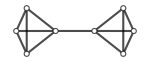
A particle can travel on a graph. 
-Graphics-
Let i denotes the state that the particle stays on the ith vertex of the graph. The following operator
Ĥ=-∑_(i<->j) (ij+ji) 
describes the quantum process for the particle to tunnel from one vertex to the adjacent vertex (the summation sums over all links i<->j on the graph).
(i) Represent the operator Ĥ as a matrix in the basis of {i}.
(ii) Write a computer program to compute the lowest and second lowest eigenvalues.
(iii) Visualizing the corresponding eigen vectors by marking the vector components on the graph. What do you find?
[Comment: quantum mechanics can be applied to classify vertices on a graph --- an algorithm known as the spectral clustering.]

#### Eigensystem (Pauli Operators)

Example: Eigenvalues and eigenvectors of Pauli operators

Pauli matrices are 2×2 Hermitian matrices. Each one has two distinct eigenvalues, and two corresponding orthogonal eigenvectors.

opertor | (σ̂)^x |  | (σ̂)^y |  | (σ̂)^z | 
(matrix) | (0 | 1
1 | 0) |  | (0 | -ⅈ
ⅈ | 0) |  | (1 | 0
0 | -1) | 
eigenvalue | +1 | -1 | +1 | -1 | +1 | -1
eigenvector | + | - | ⅈ | ⅈ̄ | 0 | 1
(vector) | 1/(√2)(1
1) | 1/(√2)(1
-1) | 1/(√2)(1
ⅈ) | 1/(√2)(1
-ⅈ) | (1
0) | (0
1)
projector | ++ | -- | ⅈⅈ | ⅈ̄ⅈ̄ | 00 | 11
(matrix) | 1/2(1 | 1
1 | 1) | 1/2(1 | -1
-1 | 1) | 1/2(1 | -ⅈ
ⅈ | 1) | 1/2(1 | ⅈ
-ⅈ | 1) | (1 | 0
0 | 0) | (0 | 0
0 | 1)

Spectral decompositions:

Pauli-x

(σ̂)^x=++---,

with projection operators

++=(𝟙+(σ̂)^x)/2,
--=(𝟙-(σ̂)^x)/2.

Pauli-y

(σ̂)^y=ⅈⅈ-ⅈ̄ⅈ̄,

with projection operators

ⅈⅈ=(𝟙+(σ̂)^y)/2,
ⅈ̄ⅈ̄=(𝟙-(σ̂)^y)/2.

Pauli-z

(σ̂)^z=00-11,

with projection operators

00=(𝟙+(σ̂)^z)/2,
11=(𝟙-(σ̂)^z)/2.

In general, the Pauli operator n·σ̂ along the direction of the unit vector n has the following spectral decomposition

n·σ̂=n·σ=+1n·σ=+1-n·σ=-1n·σ=-1,

with the projection operators

n·σ=±1n·σ=±1=(𝟙±n·σ̂)/2.

Prove Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

Given that n·σ̂ is a 2×2 Hermitian matrix, it must have two real eigenvalues, denoted as λ_1 and λ_2. In the eigenbasis, n·σ̂ is represented as a diagonal matrix

n·σ̂≏(λ_1 | 0
0 | λ_2)

Notice that

λ_1+λ_2=Tr (n·σ̂)=0,
(λ_1^2 | 0
0 | λ_2^2)≏(n·σ̂)^2=𝟙,

we have

λ_1^2=λ_2^2=1⇒λ_1,λ_2=±1,
λ_1+λ_2=0⇒λ_1=-λ_2.

So the two eigenvalues of n·σ̂ must be +1 and -1, and the spectral decomposition must take the form of

n·σ̂=n·σ=+1n·σ=+1-n·σ=-1n·σ=-1,

In the eigenbasis, without loss of generality, we can write

n·σ̂≏(1 | 0
0 | -1).

Now the projectors are represented as

n·σ=+1n·σ=+1≏(1 | 0
0 | 0), 
n·σ=-1n·σ=-1≏(0 | 0
0 | 1).

Comparing Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered), we conclude

n·σ=±1n·σ=±1,=(𝟙±n·σ̂)/2.

To check this result, substitute Eq. (DisplayFormulaNumbered) into Eq. (DisplayFormulaNumbered), we can see that the equation is consistent.

### Observables

#### Physical Observable

Postulate 2 (Observables): Physical observables of a quantum system are described by Hermitian operators (represented as Hermitian matrices) acting on the associated Hilbert space.

Consider a Hermitian operator Ô with eigenvalues O_k and eigenvectors O_k (m=1,2,…,g_k), i.e.

Ô=∑_k O_k O_k O_k.

The operator Ô corresponds to a physical observable O in the sense that

All possible measurement outcomes (or observation values) of the observable O are given by (and only by) the eigenvalues O_k.

The measurement projects (collapses) the quantum state to the eigenspace ℋ_k spanned by the eigenstates of the corresponding measurement outcome O_k.

#### Measurement Postulate

Postulate 3 (Measurement): Given a quantum system in the state ψ and the observable O to be measured: 
(i) the probability to observe the measurement outcome O_k is p(O_k|ψ)=(|O_kψ|)^2, 
(ii) if O_k is observed, the state will collapse to O_k.

In quantum measurement, there is no way to tell for certain which outcome will be observed. There is only a conditional probability p(O_k|ψ) that we can predict.

Upon observing the measurement outcome O_k, the quantum state will be updated --- a process known as quantum state collapse.

ψ(⟶^(measure O))_(observe O_k)O_k.

ψ is called the prior state (pre-measurement state)

O_k is called the posterior state (post-measurement state)

Bayesian view of quantum state collapse:

The quantum state represents our subjective knowledge or belief about the system, not (necessarily) an objective physical reality.

Measurements provide new information that forces us to update our beliefs → the “collapse” happens in our knowledge.

The measurement postulate tells us how to update the quantum state given the observation, in a logically consistent manner.

How to deal with degeneracy?

An eigenvalue O_k is n-fold degenerated ⇔ there exists n orthonormal eigenstates (their choices are not unique) of Ô corresponding to the same eigenvalue:

Ô O_k,1=O_k O_k,1,
Ô O_k,2=O_k O_k,2,
…
Ô O_k,n=O_k O_k,n.

Then if the measurement outcome O_k is observed in measuring O on state ψ, how to compute p(O_k|ψ) and the posterior state?

Step I: Compute the scalar products α_m=O_k,mψ, meaning that

ψ=∑_(m=1)^n α_m O_k,m+… (other states).

Step II: Aggregate the probability:

p(O_k|ψ)=∑_(m=1)^n (|α_m|)^2=∑_(m=1)^n (|O_k,mψ|)^2.

Step III: Renormalize the amplitudes α_m

(α̃)_m=α_m/(√(p(O_k|ψ)))=(O_k,mψ)/(√(p(O_k|ψ))),

and reconstruct the posterior state

ψ(⟶^(measure O))_(observe O_k)ψ'=∑_(m=1)^n (α̃)_m O_k,m.

Note: it is always a good practice to normalize the state (i.e. ensuring ψ'ψ'=1) after quantum state collapse.

Let {1,2,3} be a set of orthonormal basis of a three-state system. Suppose the system is in the prior state ψ=1/(√3)(1+2+3).
Consider measuring the observable Ô=12+21-33.  
(i) What are the possible measurement outcomes (observation values)?
(ii) What are the probabilities to observe each outcome?
(iii) What posterior states will the system collapse to after observing each outcome?

#### Expectation Value

The expectation value of an observable O, denoted as ⟨O⟩, is the averaged measurement outcome of O over many repeated experiments (with the same prior state ψ prepared each time).

According to the measurement postulate

⟨O⟩:=∑_k O_k p(O_k|ψ)
=∑_k O_k(|O_kψ|)^2
=∑_k ψO_k O_k O_kψ

Given Ô=∑_k O_k O_k O_k, we conclude

⟨O⟩=ψ Ô ψ.

The answer is a real scalar (as Ô is Hermitian).

Represented as vectors and matrices,

⟨O⟩=(ψ_1^* | ψ_2^* | ⋯)(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱)(ψ_1
ψ_2
⋮).

Alternatively, the expectation value can also be written as a trace of the product of the observable operator Ô and the state projector ψψ

⟨O⟩=Tr Ô ψψ.

The advantage of this approach is to circumvent solving for ψ explicitly (sometimes the state projector is easier to construct than the state vector).

Let m and n be three-component real unit vectors. For a qubit, consider measuring n·σ on the m·σ=+1 state.
(i) What is the probability to observe n·σ=+1?
(ii) What is the expectation value of the operator n·σ̂ on the state  m·σ=+1?
[Express your results in terms of m and n. Hint: using Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) can simplify the calculation.]

#### Variance

The variance of an observable O on a state ψ is defined as

var O=⟨(O-⟨O⟩)^2⟩=⟨O^2⟩-⟨O⟩^2.

where ⟨O^2⟩=ψ(Ô)^2 ψ and ⟨O⟩=ψ Ô ψ. The square root of the variance defines the standard deviation:

std O=√(var O).

Uncertainty Relation: for any pair of observables A and B measured on any given state (repeatedly),

(std A)(std B)≥1/2|⟨[A,B]⟩|.

Prove Eq. (DisplayFormulaNumbered).

Suppose Â and B̂ are Hermitian operators. Let ϕ=(Â+ⅈ x B̂)ψ. For any choice of x∈ℝ,

ψ(Â-ⅈ x B̂)(Â+ⅈ x B̂)ψ=ϕϕ≥0.

On the other hand,

ψ(Â-ⅈ x B̂)(Â+ⅈ x B̂)ψ
=ψ(Â)^2+ⅈ x [Â,B̂]+x^2(B̂)^2 ψ
=⟨B^2⟩x^2+ⅈ⟨[A,B]⟩x+⟨A^2⟩≥0.

The quadratic equation ⟨B^2⟩x^2+ⅈ⟨[A,B]⟩x+⟨A^2⟩=0 has no (or only one) real root, implying that its discriminant Δ must be negative (or zero), i.e.

Δ=(ⅈ⟨[A,B]⟩)^2-4⟨B^2⟩⟨A^2⟩≤0.

Therefore for any A,B on any state ψ,

⟨A^2⟩^(1/2)⟨B^2⟩^(1/2)≥1/2|⟨[A,B]⟩|.

The uncertainty relation Eq. (DisplayFormulaNumbered) can be shown by replacing Â→Â-⟨A⟩𝟙 and B̂→B̂-⟨B⟩𝟙, which does not affect the assumption of this proof.

In words, the product of the uncertainties cannot be smaller than half of the magnitude of the expectation value of the commutator.

For commuting observables ([A,B]=0), (std A)(std B)≥0, it is possible to have std A=std B=0 simultaneously, i.e. A and B can be jointly measured with perfect certainty.

For non-commuting observables, there exists a state on which |⟨[A,B]⟩|≠0. Then on such state, it is impossible to have std A=std B=0 simultaneously, i.e. A and B can not be jointly measured with certainty.

## Dynamics

### Unitary Operators

#### Basis Transformation

Suppose we have two sets of orthonormal basis of the same Hilbert space ℋ

ℬ={i:i=1,2,…,dim ℋ},
ℬ'={i':i=1,2,…,dim ℋ}.

For example, the eigen basis of (σ̂)^x v.s. that of (σ̂)^z.

The same state v can have different vector representations in different bases

v_i=iv, v'_i=i' v.

The same operator Ô can have different matrix representations in different bases

O_ij=i Ô j, O'_ij=i' Ô j'.

How are representations in different bases related? - Basis transformation. Basis transformation from ℬ to ℬ' is describe by a matrix U with the matrix element

U_ij=i' j.

such that the representation in the new basis is related to that in the old basis by

v'_i=∑_j U_ij v_j,
O'_ij=∑_(k,l) U_ik O_kl U_jl^*.

Using Eq. (DisplayFormulaNumbered) to prove that Eq. (DisplayFormulaNumbered) is compatible with Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

Basis transformation for state

v'_i=∑_j U_ij v_j
=∑_j i' jjv
=i' 𝟙v
=i' v.

Basis transformation for operator

O'_ij=∑_(k,l) U_ik O_kl U_jl^*
=∑_(k,l) i' kk Ô ll j'
=i' 𝟙 Ô 𝟙 j'
=i' Ô j'.

In quantum mechanics, every operator is a matrix, and every matrix is an operator. So does the basis transformation matrix.

Û=∑_i ii'.

Check that the matrix element of Û in Eq. (DisplayFormulaNumbered) is indeed given by Eq. (DisplayFormulaNumbered), regardless of represented in the basis ℬ or ℬ'.

When represented in ℬ, the matrix element of Û should be given by Eq. (DisplayFormulaNumbered) as

U_ij=i Û j
=∑_k ik k' j
=∑_k δ_ik k' j
=i' j.

When represented in ℬ',

U'_ij=i' Û j'
=∑_k i' k k' j'
=∑_k i' k δ_kj
=i' j.

It turns out that the matrix elements U'_ij=U_ij are the same regardless of basis (this is a special property for the basis transformation matrix between two orthonormal bases).

Û in Eq. (DisplayFormulaNumbered) is an example of the unitary operator.

A operator Û is unitary, iff

(Û)^†Û=Û(Û)^†=𝟙.

Check that Eq. (DisplayFormulaNumbered) satisfies the defining property Eq. (DisplayFormulaNumbered) for unitary operator.

(Û)^†Û=∑_i i' i∑_j j j'
=∑_(i,j) i' ij j'
=∑_(i,j) i' δ_ij j'
=∑_(i,j) i' i'=𝟙.

Similarly U U^†=𝟙.

The inverse of a unitary operator is its Hermitian conjugate

(Û)^-1=(Û)^†.

The operator (basis transformation) implemented by Û is reversed by that of (Û)^†, and vice versa.

When the two sets of basis i and i' are identical, U=𝟙 becomes the identity operator (which is also unitary).

In terms of the unitary operator, the basis transformation Eq. (DisplayFormulaNumbered) can be written as

for ket state: | v→Û v,
for bra state: | v→v(Û)^†,
for operator: | Ô→Û Ô (Û)^†.

The operator Ô is also made of ket and bra states, so the unitary operator must be applied from both sides, when transforming an operator.

The expectation value of an observable is invariant under basis transformation. (Physical reality should be basis-independent.)

⟨O⟩=ψ Ô ψ→ψ(Û)^† Û Ô (Û)^†Û ψ=ψ𝟙 Ô 𝟙ψ=⟨O⟩.

#### Matrix Diagonalization

Diagonalization of a Hermitian operator: find a unitary operator Û to bring the Hermitian operator Ô to diagonal form by transforming to its eigenbasis.

Ô=∑_k O_k O_k O_k,
Û=∑_k kO_k,

such that under Ô→Û Ô (Û)^†,

Λ̂=Û Ô (Û)^†=∑_k k O_k k≏(O_1 |   |  
  | O_2 |  
  |   | ⋱)

is diagonal in the basis of one-hot vectors k.

Every Hermitian matrix can be written as

Ô=(Û)^†Λ̂ Û,

with Λ̂ being diagonal and Û being unitary.

Or equivalently, the unitary transformation Û brings the Hermitian matrix to its diagonal form,

Û Ô (Û)^†=Λ̂.

Example: diagonalization of Pauli matrix

The Pauli matrix (σ̂)^x can be diagonalized by the following unitary transformation (whose row vectors are bra eigenvectors of (σ̂)^x)

(Û)_H=(+
-)≏1/(√2)(1 | 1
1 | -1).

This unitary operation (Û)_H is also known as the Hadamard gate in quantum information, an example of single-qubit gate.

Under the unitary transformation, (σ̂)^x is brought to its diagonal form, which is (σ̂)^z

(Û)_H (σ̂)^x (Û)_H^†≏1/(√2)(1 | 1
1 | -1)(0 | 1
1 | 0)1/(√2)(1 | 1
1 | -1)
=(1 | 0
0 | -1)≏(σ̂)^z.

#### Hermitian Generators

If Hermitian operators are generalization of real numbers, then unitary operators are generalization of phase factors.

A complex number z∈ℂ is a phase factor, iff |z|=1. Any phase factor can be written as z=ⅇ^(ⅈ θ), where θ∈ℝ is a real phase angle.

z^*z=z z^*=(|z|)^2=1⇔z=ⅇ^(ⅈ θ)

Similar ideas apply to unitary operators: every unitary operator can be generated by a Hermitian operator Θ̂ in the form of

Û=ⅇ^(ⅈ Θ̂).

Given a Hermitian operator Θ̂

Θ̂=∑_k Θ_k Θ_k Θ_k,

by ⅇ^(ⅈ Θ̂) we mean

either by operator Taylor expansion Eq. (DisplayFormulaNumbered)

ⅇ^(ⅈ Θ̂)=𝟙+ⅈ Θ̂+(ⅈ Θ̂)^2/(2!)+(ⅈ Θ̂)^3/(3!)+….

or by spectral decomposition (HW Homework)

ⅇ^(ⅈ Θ̂)=∑_k Θ_k ⅇ^(ⅈ Θ_k)Θ_k

Don’t do element-wise exponentiation on the matrix!

Use Eq. (DisplayFormulaNumbered) to show that Û=ⅇ^(ⅈ Θ̂) is unitary as long as Θ̂ is Hermitian.

(Û)^†Û=(ⅇ^(ⅈ Θ̂))^†ⅇ^(ⅈ Θ̂)
=(∑_k ⅇ^(ⅈ Θ_k)Θ_kΘ_k)^†(∑_l ⅇ^(ⅈ Θ_l)Θ_lΘ_l)
=∑_(k,l) ⅇ^(-ⅈ Θ_k)ⅇ^(ⅈ Θ_l)Θ_kΘ_kΘ_lΘ_l
=∑_(k,l) ⅇ^(-ⅈ Θ_k)ⅇ^(ⅈ Θ_l)Θ_kΘ_k δ_kl
=∑_k ⅇ^(-ⅈ Θ_k)ⅇ^(ⅈ Θ_k)Θ_kΘ_k
=∑_k Θ_kΘ_k
=𝟙.

and similar for Û (Û)^†=𝟙.

Example: unitary generated by Pauli matrix. Recall Û(θ)=e^(ⅈ θ (σ̂)^y) in (Exc Exercise).

Û(θ)=ⅇ^(ⅈ θ (σ̂)^y)≏(cos θ | sin θ
-sin θ | cos θ).

It implements a basis rotation with θ being the rotation angle:

Û(θ)0≏(cos θ | sin θ
-sin θ | cos θ)(1
0)=(cos θ
-sin θ).

Special case: when θ=0, Û(0)=𝟙 ⇒ no rotation is performed.

More generally, let Û(θ) be the unitary operator that implements certain basis rotation by a real angle θ. When θ=Δθ is small, we can Taylor expand

Û(Δθ)=Û(0)+Û'(0)Δθ+…=𝟙+Û'(0)Δθ+…,

where Û'(0) is ∂_θ Û(θ) evaluated at θ=0.

Û'(0) is also an operator (matrix), usually denoted as Û'(0)=ⅈ Ĝ. We call Ĝ the generator of the rotation/unitary operator, because it generates an infinitesimal rotation

Û(Δθ)=𝟙+ⅈ Δθ Ĝ+....

Û(Δθ) is unitary ⇒ Ĝ is Hermitian.

(U(Δθ))^†U(Δθ)
=(𝟙-ⅈ Δθ (Ĝ)^†+...)(𝟙+ⅈ Δθ Ĝ+...)
=𝟙+ⅈ Δθ(Ĝ-(Ĝ)^†)+…=𝟙.

Large rotations can be accumulated from small rotations.

Û(N Δθ)=(Û(Δθ))^N=(𝟙+ⅈ Δθ Ĝ)^N.

As Δθ is small (but N can be large, s.t. θ=N Δθ is finite),

ln Û(N Δθ)=N ln(𝟙+ⅈ Δθ Ĝ)=ⅈ N Δθ Ĝ,

So Û(N Δθ)=ⅇ^(ⅈ N Δθ Ĝ), we obtain the exponential form

Û(θ)=ⅇ^(ⅈ θ Ĝ).

Conclusion: every Hermitian operator Θ̂=θ Ĝ generates a unitary operator ⅇ^(ⅈ Θ̂) by the exponential map.

### Time Evolution

#### Time-Evolution is Unitary

Unitarity: information is never lost!

Basic assumption: quantum information is preserved under quantum dynamics, i.e. two identical and isolated systems

start out in different states ⇒ remains in different states (towards both future and past).

start out in the same state ⇒ follow identical evolution (towards both future and past).

Although measurement seems to be non-deterministic, evolution of quantum state is deterministic: suppose you know the state at one time, then the quantum equation of motion tell you what it will be later.

ψ(t)=Û(t)ψ(0),

ψ(0) is the initial state, and ψ(t) is the state at time t. Û(t) is the time-evolution operator that takes ψ(0) to ψ(t). ☟We will show that Û(t) should be unitary.

Distinct states remain distinct:

ϕ(0)ψ(0)=0⇒ϕ(t)ψ(t)=ϕ(0)(Û(t))^†Û(t)ψ(0)=0.

Identical states remain the identical:

ψ(0)ψ(0)=1⇒ψ(t)ψ(t)=ψ(0)(Û(t))^†Û(t)ψ(0)=1.

Or, the fact that the probability adds up to 1 must be preserved.

Treat ψ(0) and ϕ(0) as members of any orthonormal basis, then Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) implies

i(Û(t))^†Û(t)j=δ_ij⇒(Û(t))^†Û(t)=𝟙.

Therefore, the time-evolution operator Û(t) is unitary.

#### Hamiltonian

Hamiltonian generates time-evolution!

As a unitary operator, the time-evolution operator is also generated by a Hermitian operator, called the Hamiltonian,

Ĥ=ⅈ Û'(0)=ⅈ ∂_t Û(t)|_(t=0).

For small Δt, infinitesimal evolution is given by

Û(Δt)=𝟙-ⅈ Ĥ Δt+...,

therefore the state evolves as

ψ(Δt)=Û(Δt)ψ(0)=ψ(0)-ⅈ Δt Ĥ ψ(0),

meaning that

ⅈ ∂_t ψ(0)=ⅈ (ψ(Δt)-ψ(0))/Δt=Ĥ ψ(0).

There is nothing special about t=0. Eq. (DisplayFormulaNumbered) should hold at any time.

ⅈ∂_t ψ(t)=Ĥ ψ(t).

This is the Schrödinger equation, the equation of motion for the quantum state.

The Hamiltonian Ĥ(t)=ⅈ Û'(t) can be time-dependent in general.

But in many cases, we consider Ĥ to be time-independent, by assuming the time-translation symmetry.

What happens to Planck’s constant?

ℏ=h/(2π)=1.0545718(13)×10^-34 J s.

In quantum mechanics, the observable associated with the Hamiltonian is the energy. To balance the dimensionality across the Schrödinger equation, Planck’s constant is inserted for Eq. (DisplayFormulaNumbered):

ⅈ ℏ∂_t ψ(t)=Ĥ ψ(t).

Why is ℏ so small? Well, the answer has more to do with biology than with physics ⇒ Why we are so big, heavy and slow? A natural choice for quantum mechanics is to set the units such that ℏ=1. It is a common practice in theoretical physics (we will also use this convention sometimes).

#### Schrödinger Equation: State Dynamics

Postulate 4 (Dynamics): The time-evolution of the state of a quantum system is governed by the Hamiltonian of the system, according to the time-dependent Schrödinger equation.

ⅈ ℏ∂_t ψ(t)=Ĥ ψ(t).

If the Hamiltonian Ĥ is time-independent, we can first find its eigenvalues (or eigen energies) and eigenvectors (or energy eigenstates).

Ĥ E_k=E_k E_k.

This is also called the time-independent Schrödinger equation. Without solving a differential equation, we just need to diagonalize a Hermitian matrix in this case.

Each energy eigenstate will evolve in time simply by a rotating overall phase,

E_k(t)=ⅇ^(-ⅈ/ℏ E_k t)E_k.

E_k form a complete set of orthonormal basis, called energy eigenbasis.

Verify that Eq. (DisplayFormulaNumbered) is a solution of Eq. (DisplayFormulaNumbered):

Left-hand side:

ⅈ ℏ∂_t E_k(t)=ⅈ ℏ∂_t (ⅇ^(-ⅈ/ℏ E_k t)E_k)
=ⅈ ℏ∂_t (ⅇ^(-ⅈ/ℏ E_k t))E_k
=E_k ⅇ^(-ⅈ/ℏ E_k t)E_k
=E_k E_k(t),

Right-hand side:

Ĥ E_k(t)=ⅇ^(-ⅈ/ℏ E_k t)Ĥ E_k
=ⅇ^(-ⅈ/ℏ E_k t)E_k E_k
=E_k E_k(t).

So the two sides matches.

Any initial state ψ(0) will evolve in time by first representing the initial state in the energy eigenbasis, and attaching to each energy eigenstate by its rotating overall phase,

ψ(t)=∑_i ⅇ^(-ⅈ/ℏ E_i t)E_iE_iψ(0)
=ⅇ^(-ⅈ/ℏ Ĥ t)ψ(0).

A time-independent Hamiltonian generates the time-evolution via matrix exponentiation

Û(t)=exp(-ⅈ/ℏ Ĥ t).

However, for time-dependent Hamiltonian, there no such a clean formula. Evolution must be carried out step by step, denoted as a time-ordered exponential

Û(t)=𝒯 exp(-ⅈ/ℏ∫_0^t Ĥ(t')ⅆ t').

##### Larmor Precession and Rabi Oscillation

How to write down a Hamiltonian?

derive it from experiment,

borrow it from some theory we like,

pick one and see what happens.☜

Hamiltonian must be Hermitian anyway. For a single spin (qubit), the most general Hamiltonian takes the form of

Ĥ=h_0 𝟙+h_x(σ̂)^x+h_y(σ̂)^y+h_z(σ̂)^z
=h_0 𝟙+h·σ̂,

where h_0,h_x,h_y,h_z∈ℝ are all real coefficients.

The time-evolution operator (set ℏ=1 in the following)

Û(t)=ⅇ^(-ⅈ Ĥ t)
=ⅇ^(-ⅈ h_0 t)(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂),

where |h|=√(h·h) and h̃=h/|h|.

Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

Given Ĥ=h_0 𝟙+h·σ̂,

Û(t)=ⅇ^(-ⅈ Ĥ t)
=ⅇ^(-ⅈ (h_0 𝟙+h·σ̂) t)
=ⅇ^(-ⅈ h_0 t)exp(-ⅈ |h|h̃·σ̂ t)
=ⅇ^(-ⅈ h_0 t)(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂).

The last step is by Taylor expansion and using the fact that (h̃·σ̂)^2=𝟙. The problem maps to (HW Homework) by n=h̃ and θ=-|h|t.

A state ψ(0) will evolve with time following

ψ(t)=Û(t)ψ(0)
=ⅇ^(-ⅈ h_0 t)(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂)ψ(0).

If we measure σ on the state ψ(t), the expectation value will be given by

⟨σ⟩_t=ψ(t)σ̂ ψ(t)
=cos(2|h|t)⟨σ⟩_0+sin(2|h|t)h̃×⟨σ⟩_0+(1-cos(2|h|t))h̃(h̃·⟨σ⟩_0).

which also evolves with time.

Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).
Hint: Eq. (DisplayFormulaNumbered) can make life much more easier.

Instead of evaluating ⟨σ⟩_t, we first consider m·⟨σ⟩_t

m·⟨σ⟩_t=ψ(t)m·σ̂ψ(t)=ψ(0)(cos(|h|t)𝟙+ⅈ sin(|h|t)h̃·σ̂)m·σ(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂)ψ(0).

The operator inside the bracket reads

(cos(|h|t)𝟙+ⅈ sin(|h|t)h̃·σ̂)m·σ̂(cos(|h|t)𝟙-ⅈ sin(|h|t)h̃·σ̂)
=cos^2(|h|t)m·σ̂+ⅈ sin(|h|t)cos(|h|t)(h̃·σ̂ m·σ̂-m·σ̂h̃·σ̂)+sin^2(|h|t)h̃·σ̂ m·σ̂h̃·σ̂.

Given a·σ̂ b·σ̂=a·b 𝟙+ⅈ (a×b)·σ̂, we have

h̃·σ̂ m·σ̂=h̃·m 𝟙+ⅈ (h̃×m)·σ̂,
m·σ̂h̃·σ̂=ĥ·m 𝟙-ⅈ (h̃×m)·σ̂,
h̃·σ̂ m·σ̂h̃·σ̂=h̃·m h̃·σ̂+ⅈ (h̃×m)·σ̂h̃·σ̂
=h̃·m h̃·σ̂+ⅈ((h̃×m)·h̃𝟙+ⅈ((h̃×m)×h̃)·σ̂)
=h̃·m h̃·σ̂-((h̃×m)×h̃)·σ̂
=h̃·m h̃·σ̂-(h̃·h̃m·σ̂-h̃·mh̃·σ̂)
=2h̃·m h̃·σ̂-m·σ̂.

Eq. (DisplayFormulaNumbered) becomes

cos^2(|h|t)m·σ̂-2 sin(|h|t)cos(|h|t) (h̃×m)·σ̂+sin^2(|h|t)(2h̃·m h̃·σ̂-m·σ̂)
=cos(2|h|t)m·σ̂+sin(2|h|t)m· (h̃×σ̂)+(1-cos(2|h|t))h̃·m h̃·σ̂.

Plugging back to Eq. (DisplayFormulaNumbered)

m·⟨σ⟩_t=cos(2|h|t)m·⟨σ⟩_0+sin(2|h|t)m· (h̃×⟨σ⟩_0)+(1-cos(2|h|t))h̃·m h̃·⟨σ⟩_0.

Now we take derivatives with respect to m on both sides to get Eq. (DisplayFormulaNumbered).

Larmor precession: assume h=(0,0,h_z) along the z-direction, and parameterize the expectation of the spin vector by ⟨σ⟩=(sin θ cos φ,sin θ sin φ,cos θ).

⟨σ⟩_t=(sin θ_0 cos (φ_0+2 h_z t), sin θ_0 sin(φ_0+2 h_z t),cos θ_0),

where θ_0 and φ_0 are the initial azimuthal and polar angles.

The solution describes the spin ⟨σ⟩ precessing around the axis of the Zeeman field h.

```mathematica
Block[{θ=π/4},Graphics3D[{EdgeForm[None],{Red,Sphere[{0,0,0},0.4],Tube[#{-Sin[θ],0,Cos[θ]}&/@{-1,0.6},0.1],Cone[#{-Sin[θ],0,Cos[θ]}&/@{0.6,1.5},0.2],Text["\!\(⟨σ⟩\)",1.5{-Sin[θ],0,Cos[θ]},{1,-0.5}]},
{Blue,Tube[{0,0,#}&/@{-1.5,1.5},0.05],Cone[{0,0,#}&/@{1.5,2},0.1],Text[Style["\!\(h\)",Bold],{0,0,2},{0,-0.5}]},
{Arrowheads[{0.08,#}&/@{0.25,0.5,0.75}],Dashed,Arrow[Table[1.5{-Sin[θ]Cos[ϕ],-Sin[θ]Sin[ϕ],Cos[θ]},{ϕ,0,2π,π/32}]]}},Lighting->"Neutral",Boxed->False,ImageSize->80]]
```

-Graphics3D-

The precession frequency ω=2|h| is called the Larmor frequency. It can be used to probe the local Zeeman field strength, which has applications in nuclear magnetic resonance (NMR) and nitrogen-vacancy (NV) center.

Energy of a spin in the Zeeman field is ⟨H⟩=-h·⟨σ⟩ (up to some constant energy shift h_0).

Rabi oscillation: a qubit initially prepared in state 0, evolved under the Hamiltonian

Ĥ=Ω (σ̂)^x+Δ (σ̂)^z≏(Δ | Ω
Ω | -Δ),

where Ω is the driving field and Δ is called detuning. The probability to find the qubit in state 1 at time t is given by

(p(1|0))_t=⟨𝒫_1⟩_t=(1-⟨σ^z⟩_t)/2=(sin^2(ω t/2))/(1+(Δ/Ω)^2),

with the Rabi frequency ω=2 √(Ω^2+Δ^2).

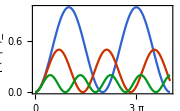
-Graphics--Graphics- | Δ/Ω=0
-Graphics- | Δ/Ω=1
-Graphics- | Δ/Ω=2

```mathematica
Row@{Plot[Evaluate@Table[Sin[Sqrt[1+Δ^2] Ωt/2]^2/(1+Δ^2),{Δ,{0,1,2}}],{Ωt,0,4π},FrameLabel->{"\!\(Ω t\)","\!\(p(1|0)\_t\)"},FrameTicks->{{Automatic,Automatic},{π Range[0,4],None}},GridLines->{π Range[0,4],{0,1}},BaselinePosition->Scaled[0.64],ImageSize->180],
Grid[{Graphics[{#1,Line[{{0,0},{1,0}}]},AspectRatio->0.1,ImageSize->20],Style[StringTemplate["\!\(Δ/Ω=`1`\)"][#2],FontFamily->"CMU"]}&@@@{{Blue,0},{Red,1},{Green,2}},Spacings->{Automatic, 0.1}]}
```

Rabi π-Pulse: flipping 0 to 1 (and vice versa) by a π-pulse (turn on the driving field Ω for time t=π/Ω and turn off) at resonance Δ=0. This implements a NOT gate (or X gate) on a single qubit.

#### Heisenberg Equation: Operator Dynamics

Two pictures of the quantum dynamics:

Schrödinger picture: state evolves in time, operator remains fixed,

⟨O(t)⟩=ψ(t)Ô ψ(t).

Heisenberg picture: operator evolves in time, state remains fixed,

⟨O(t)⟩=ψÔ(t)ψ.

The two pictures are consistent, if

ψ(t)=Û(t)ψ⇒Ô(t)=(Û(t))^†Ô Û(t),

such that Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) are consistent, as they both implies

⟨O(t)⟩=ψ(Û(t))^†Ô Û(t)ψ.

Note: one should only apply one picture at a time, i.e. either the state or the operator is time-dependent, but not both.

In the Heisenberg picture, the time-evolution of an operator

Ô(t)=(Û(t))^†Ô Û(t),

described by the Heisenberg equation

ⅈ ℏ∂_t Ô(t)=[Ô(t),Ĥ].

Derive Eq. (DisplayFormulaNumbered) from Eq. (DisplayFormulaNumbered).

For small Δt (with ℏ=1)

Ô(Δt)=(Û(Δt))^†Ô Û(Δt)
=e^(ⅈ Ĥ Δt)Ô e^(-ⅈ Ĥ Δt)
=(𝟙+ⅈ Ĥ Δt+…)Ô (𝟙-ⅈ Ĥ Δt+…)
=Ô+ⅈ (Ĥ Ô-Ô Ĥ) Δt+…
=Ô-ⅈ [Ô,Ĥ] Δt+…

therefore

ⅈ ∂_t Ô=ⅈ(Ô(Δt)-Ô)/Δt=[Ô,Ĥ].

Restore ℏ, we arrive at Eq. (DisplayFormulaNumbered).

Correspondingly, its expectation value evolves as

ⅈ ℏ∂_t ⟨O(t)⟩=⟨[Ô(t),Ĥ]⟩.

If [Ô,Ĥ]=0, the Heisenberg equation Eq. (DisplayFormulaNumbered) implies that ∂_t ⟨O⟩=0, i.e. O will be invariant in time. The observable O is a conserved quantity (or an integral of motion) if Ô commutes with the Hamiltonian Ĥ.

Consider a single-qubit Hamiltonian H=h·Ŝ, where Ŝ=ℏ/2 σ̂ is the spin operator.
(i) Show that the expectation values of the spin operator evolves as ∂_t ⟨S⟩=h×⟨S⟩.
(ii) Show that
⟨S(t)⟩=cos(|h|t)⟨S(0)⟩+sin(|h|t)h̃×⟨S(0)⟩+(1-cos(|h|t))h̃(h̃·⟨S(0)⟩)
is a solution of ∂_t ⟨S⟩=h×⟨S⟩, where h̃=h/|h|.
This describes the dynamics of a spin in a Zeeman field h.
(iii) Show that the spin component along the Zeeman field h̃·S is a conserved quantity.